# Regression modelling of precision matrix

## Full rank case

### Generate data

```mathematica
(* Batch dimension is last one *)
n=2;
e=0.01;
cov={{1, 1-e},{1-e,1}};
zero=0&/@Range@n;
normal=MultinormalDistribution[zero,cov];
pdf[x_,y_]=PDF[normal,{x,y}];
dsize=1000;
SeedRandom[0];
X=RandomVariate[normal,{dsize}]//Transpose;
(* center the data *)
Xc=Mean[Transpose@X];
X=Transpose[#-Xc&/@Transpose[X]];
wt = {{1,1}}; (* true w *)
w0={{2,1}}; (* initial w *)
Y=Dot[wt, X];
XY = X~Join~Y;
grad[w_]:=2(w.X-Y).Transpose[X]/dsize;
loss[w_]:=Module[{error},
error=(w.X-Y);
First[Flatten[error.errorᵀ/dsize]]
];
Print["Loss at w0 ",loss[w0]];
Print["Grad at w0 ",grad[w0]];
covE=X.Xᵀ/dsize; 
covE2=X.Xᵀ/(dsize-1); (* unbiased estimate *)
(* sanity checks *)
Print["True cov ",MatrixForm@cov];
Print["Empirical cov ", MatrixForm@covE];
Print["Empirical mean ", Mean@Transpose@X]
```

Loss at w0 1.03475

Grad at w0 {{2.06949,2.05021}}

True cov (1 | 0.99
0.99 | 1)

Empirical cov (1.03475 | 1.02511
1.02511 | 1.03619)

Empirical mean {-2.45359×10^-17,1.98286×10^-16}

### Modified Cholesky decomposition of covariance matrix

Use lower diagonal Cholesky as in page 64 of Pourahmadi

```mathematica
Ch=CholeskyDecomposition@covE//Transpose;
Ch//MatrixForm
```

(1.01722 | 0.
1.00775 | 0.143648)

```mathematica
Ch.Chᵀ==covE
```

True

```mathematica
Subscript[D, 1]=DiagonalMatrix@Diagonal@Ch
```

{{1.01722,0.},{0.,0.143648}}

```mathematica
L=Ch.Inverse[Subscript[D, 1]];
L//MatrixForm
```

(1. | 0.
0.990685 | 1.)

```mathematica
L.Subscript[D, 1].Subscript[D, 1].Lᵀ==covE
```

True

### Modified Cholesky decomposition of precision matrix

```mathematica
T=Inverse@L;
T//MatrixForm
```

(1. | 0.
-0.990685 | 1.)

```mathematica
Inverse[covE]==Tᵀ.Inverse[Subscript[D, 1].Subscript[D, 1]].T
```

True

#### Calculate residual variances

```mathematica
(* get decorrelated representation *)
Xnew=T.X;
```

```mathematica
Xnew.Xnewᵀ/dsize//MatrixForm
```

(1.03475 | 2.91944×10^-15
2.91944×10^-15 | 0.0206347)

```mathematica
T.covE.Tᵀ==Subscript[D, 1].Subscript[D, 1]
```

True

```mathematica
(* Residual variances are obtained from diagonal of original (unmodified) Cholesky decomposition *)
```

```mathematica
Norm[(Xnew.Xnewᵀ)/dsize-Subscript[D, 1].Subscript[D, 1]]
```

5.19001×10^-15

### Minimize using SGD

```mathematica
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimize[loss_,grad_,w0_,pre_,lr_]:=Module[{gradstep},
gradstep[w_]:=w-lr*grad[w].pre;
points=NestList[gradstep,w0,100];
loss/@points
];
```

#### No preconditioner

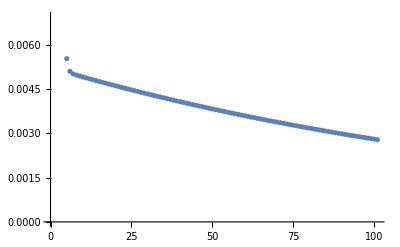

```mathematica
losses0=optimize[loss,grad,w0,IdentityMatrix[2],.15];
ListPlot@losses0
```

#### Exact Hessian as preconditioner

```mathematica
hess=D[loss[{{x,y}}],{{x,y},2}];
hess//MatrixForm
```

(2.06949 | 2.05021
2.05021 | 2.07239)

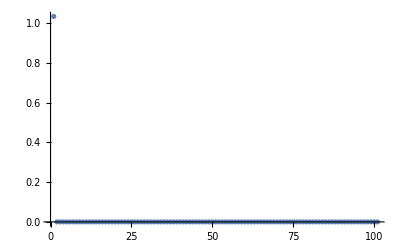

```mathematica
losses1=optimize[loss,grad,w0,Inverse@hess,1.];
ListPlot@losses1
```

#### Cholesky derived preconditioner

```mathematica
pre=Tᵀ.Inverse[Subscript[D, 1].Subscript[D, 1]].T/2;
losses2=optimize[loss,grad,w0,pre,1.];
ListPlot@losses2
```

-Graphics-

### Generate data for TF test

```mathematica
Export["~/git/whitening/exp/linear-cholesky-XY.csv",XY];
Export["~/git/whitening/exp/linear-cholesky-losses0.csv",losses0];
Export["~/git/whitening/exp/linear-cholesky-losses1.csv",losses1];
Export["~/git/whitening/exp/linear-cholesky-losses2.csv",losses2];
Export["~/git/whitening/exp/linear-cholesky-T.csv",T];
Export["~/git/whitening/exp/linear-cholesky-D1.csv",Subscript[D, 1]];
Export["~/git/whitening/exp/linear-cholesky-pre.csv",pre];
```

```mathematica
losses0[[;;10]]
```

{1.03475,0.155254,0.0270041,0.00827915,0.00552226,0.00509353,0.00500441,0.00496496,0.00493292,0.00490212}

```mathematica
losses1[[;;10]]
```

{1.03475,4.90422×10^-28,0.,0.,0.,0.,0.,0.,0.,0.}